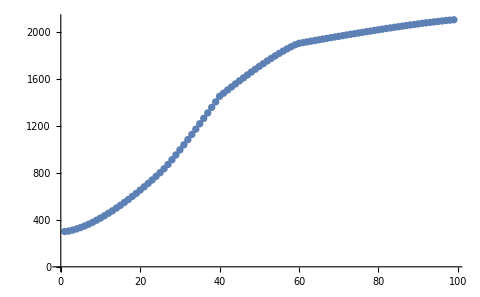

```mathematica
hpList={300,304,312,322,334,347,362,378,396,414,434,455,476,499,522,547,572,598,624,652,680,709,738,769,800,833,870,910,951,994,1037,1081,1125,1170,1216,1262,1308,1355,1402,1450,1476,1503,1529,1555,1581,1606,1631,1656,1680,1704,1727,1750,1772,1793,1814,1834,1853,1871,1887,1900,1906,1912,1918,1924,1930,1936,1942,1948,1954,1959,1965,1971,1977,1982,1988,1993,1999,2004,2010,2015,2020,2026,2031,2036,2041,2046,2051,2056,2060,2065,2070,2074,2078,2082,2086,2090,2094,2097,2100};
hpFitFunction[Lvl_]:=Piecewise[{{300+500 ((Lvl-1)/24)^1.5,1<=Lvl<=25},{800+650 ((Lvl-25)/15)^1.1,25<Lvl<=40},{1450+450(1-((60-Lvl)/20)^1.2),40<Lvl<=60},{1900+200(1-((99-Lvl)/39)^1.2),60<Lvl<=99}}];
Show[ListPlot[Table[{i,hpList[[i]]},{i,99}]],Plot[hpFitFunction[x],{x,1,99}]]
```

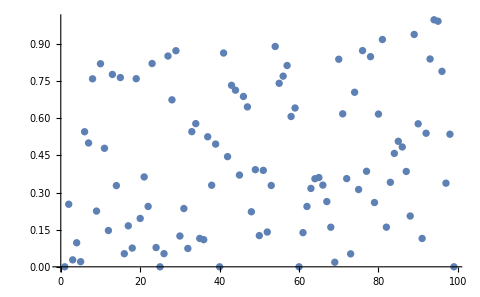

```mathematica
ListPlot[Table[{i,hpFitFunction[i]-hpList[[i]]},{i,99}]]
```